```mathematica
Clear["Global`*"]
(*Physical constants in cgs units*)
G=6.67 10^-8;  (*Newton's constant in cgs*)
c=3 10^10 ; (*Speed of light in cgs*)
κr=1.6 10^24;
kb=1.38 10^-16;
μ0=0.615;
mp=1.67 10^-24;
(*Stefan-Boltzmann constant in cgs*)
σ=5.67 10^-5;
h=6.63 10^-27;
Msun=2 10^33;
ResetDirectory[]
mydir="/home/aleksey/First_Year_Project/tlusty_tar/examples/aleksey_tlusty_runs"

B[Teff_]:=(2 h ν1^3/c^2)/(E^((h ν1)/( kb Teff))-1)
νpeak[Teff_]:=2.82 kb Teff/h


(*Calculates graybody atmosphere using Taka's formalism for a particular Teff and gravity parameter. Free is a flag to switch between the free-free and bound-free opacities*)
GrayBody[Teff_, Qg_, Free_:False, prec_:10^-8]:=Module[{κes, κs, κsb, κsf, ϵs,  ξ, f, x  , K, ϵ, Tp, Ξ, ρp, pr, pg, r, error},
κes=0.4;
(*Note that the below expression for κs assumes radiation pressure dominance. We also assume solar metallicities*)
κsb=4.7 10^20 √Qg Tp^(-15/4);
κsf=0.04 κsb;
(*If the free-free opacity dominates; Note we assume a H-He atmosphere with solar abundances*)
If[Free, κs= κsf, κs=κsb];
(*κs=1.83 10^9 √Qg(Teff)^(-9/4)*)
ϵs=κs/(κs+κes);
Ξ=(0.873 ϵs^(-1/6))/(1-0.127 ϵs^(5/6))1/(1+(ϵs^-1-1)^(2/3));
r=FindRoot[Teff^4-Ξ  Tp^4==0, {Tp, Teff}(*, EvaluationMonitor:> Print[ Tp, "  ", Tp//Im, "  ",-Ξ  Tp^4//Im] *)];

(*Plot[Teff^4- Ξ Tp^4, {Tp, 0.99 Tp/.r, 1.01 Tp/.r}]*)
(*Correction to total flux from scattering*)
Tp=Tp/.r;
x=(1+1/ϵs)^-1;
ξ=(h ν1)/(kb Teff);
f=(ξ)^-3(1-ⅇ^-ξ);
(*Solve cubic equation for the ratio of absorption opacity to scattering opacity*)
K=-1/3+2^(1/3)/(3 (-2+27 f x^2+√(-4+(-2+27 f x^2)^2))^(1/3))+((-2+27 f x^2+√(-4+(-2+27 f x^2)^2))^(1/3))/(3 2^(1/3));
(*Estimate density at the base of the photosphere for the peak frequency*)
ρp= (3 c Qg)/(4 (γ) σ Tp^4    κes^2(1+K)K)/.{ν1->νpeak[Teff], γ->4/3};
(*Estimate ratio of gas pressure to radiation pressure*)
pr=(4σ)/(3c)Tp^4;
pg= (ρp kb Tp)/(μ0 mp);
ϵ=(1+1/K)^-1//Simplify;
error=Abs[((Ξ Tp^4/.r)-Teff^4)/Teff^4];
If[error>prec, Print["Warning! Error in flux has exceeded the specified threshold. Error is ", error]];


{pr/pg, Tp, ϵ, ((Ξ Tp^4/.r)-Teff^4)/Teff^4}
]

PlotSpec[ file_:"fort.14", color_:Black,xrange_:{}, nmu_:10, mu_:1]:=Module[{dat, int, λ, ν, λh, νh, νpeak, imu, peak, prange},
SetDirectory[NotebookDirectory[]];
dat=ReadList[file, Number, RecordLists->True];
(*wavelengths in angstroms + fluxes*)
λh=Extract[dat, Position[dat, x_/;Length[x]==2]];
λh[[All, 2]]=λh[[All,2]] 4π;
νh=λh;
(*Getting frequency information*)
νh[[All,1]]=c/λh[[All, 1]] 10^8;
ν=νh[[All,1]];
peak=ν νh[[All,2]]//Max;
νpeak=ν[[(νh[[All,2]]//Ordering//#[[-1]]&)]];

(*Extract the specific intensities*)
imu=DeleteCases[dat, x_/;Length[x]==2];

imu=imu//Flatten//Partition[#, 2*nmu]&//#[[All, mu]]&;

If[xrange=={}, prange=Automatic, prange=xrange];
ListLogLogPlot[Transpose[{ν, νh[[All,2]] ν}], AxesLabel->{"ν [s^-1]", "ν F_ν [erg cm^-2 s^-1]"},  Joined->True, PlotStyle->Directive[color], PlotRange->{prange, {10^-6 peak , peak}}, PlotRangeClipping->False, ImageSize->Large]


]
Opac[ file_:"fort.85", nd_:70]:=Module[{κ, ν, dat},
SetDirectory[NotebookDirectory[]];
dat=ReadList[file, Number, RecordLists->True];
(*frequencies*)
ν=Extract[dat, Position[dat, x_/;Length[x]==2]];
ν=ν[[All,2]];
κ=DeleteCases[dat,x_/;Length[x]==2]//Flatten//Partition[#, nd]&;
Table[{ν[[i]], κ[[i]]}, {i, 1, Length[ν]}]

]
(*Parses a model atmosphere from a unit 7 input file*)
ParseAtm[file_:"fort.7"]:=Module[{atm, m,nd, blocks},
atm=ReadList[file, Number];
nd=atm[[1]];
blocks=atm[[2]];
atm=atm[[3;;]];
m=atm[[1;;nd]];
atm=atm[[nd+1;;]];
atm=Partition[atm, blocks][[All, 1;;4]];
atm=Flatten/@Transpose[{m, atm}]

]
(*Plots convergence files outputted by tlusty*)
PConv[file_:"fort.9"]:=Module[{ConvData, maxchange, maxchange2, iter, colorscale, color, colors},

ConvData=Import[file, "Table", "HeaderLines"->3]//SplitBy[#, First]&;
ConvData=Reverse/@ConvData;

maxchange=Abs[ConvData[[All, All, -3]]];
maxchange2= Max/@maxchange;

iter= ConvData//Length;
colorscale=Range[0, 1, 1/(iter-1)];
color=ColorData["Rainbow"][#]&;
colors=color/@colorscale;
GraphicsGrid[{{ListLogPlot[maxchange, Joined->True, Frame->True, PlotStyle->colors, ImageSize->Medium],
ListLogPlot[maxchange2, Joined->True, Frame->True]}}]


]
(*Plot tlusty output for flux from TLUSTY unit 13 file*)
PlotF[ file_:"fort.13", color_:Green, xrange_:{}]:=Module[{fluxdat, peak, sed, peakf, peakloc,bad, prange},
(*import data file*)
fluxdat= Import[file, "Table"][[All, 1;;2]];


fluxdat[[All,2]]=4π fluxdat[[All,2]];
sed=Transpose[{fluxdat[[All,1]],fluxdat[[All, 1]]*fluxdat[[All,2]]}];
(*Output is sometimes formatted in such a way that mathematica does not recognize it as a real number*)
bad=DeleteCases[sed, x_/;x[[2]]∈Reals];
sed=Complement[sed, bad];
(*Get location of peak for setting the range of the plot*)
If[xrange=={}, prange=Automatic, prange=xrange];
peakloc=sed[[All,2]]//Ordering//#[[-1]]&;
peak=sed[[peakloc,2]];

ListLogLogPlot[sed, Joined->True, PlotRange->{prange, {10^(- 6)peak, 2peak}},AxesLabel->{"ν [s^-1]", "ν F_ν [erg cm^-2 s^-1]"},  PlotStyle->Directive[color], ImageSize->Large]
]

(*Parses file name to infer parameters associated with the model*)
ParseFile[file_]:=Module[{s, m,t, q, sm, st, sq},
s=StringCases[file, RegularExpression["t[\-0-9]*m[\-0-9]*q[\-0-9]*"]];
st=StringCases[s, RegularExpression["t[\-0-9]*"]]//Flatten;
t=StringCases[st, "t"~~x__->x]//Flatten//#[[1]]&//ToExpression//(# 0.1)&;
sm=StringCases[s, RegularExpression["m[\-0-9]*"]]//Flatten;
m=StringCases[sm, "m"~~x__->x]//Flatten//#[[1]]&//ToExpression//(# 0.1)&;
sq=StringCases[s, RegularExpression["q[\-0-9]*"]]//Flatten;
q=StringCases[sq, "q"~~x__->x]//Flatten//#[[1]]&//ToExpression//(# 0.1)&;
{t, q, m}
]


(*Compare tlusty unit 13 file to graybody output*)
GraybodyCompare[dir_]:=
Module[{ Tp, ϵ, bb, gb, tlustyspec, gp, t, q, params, Teff, Qg}, 
params=ParseFile[dir];
t=params[[1]];
q=params[[2]];
Teff=10^t;
Qg=10^q;
(*Teff=10^4;
Qg=5.01 10^-13;*)
Tp=GrayBody[Teff, Qg][[2]];
ϵ=GrayBody[Teff, Qg][[3]];
bb=π B[Teff] ν1;
gb=π(2 ϵ^(1/2))/(1+ϵ^(1/2)) B[Tp] ν1//Re;
tlustyspec=PlotF[dir <> "/fort.13",Green,{0.1 νpeak[Teff], 10 νpeak[Teff]}];
gp=LogLogPlot[{bb, gb}, {ν1, 0.1 νpeak[Teff], 10 νpeak[Teff]}, ImageSize->Large];

Show[{tlustyspec, gp}]

]
GraybodyCompare[dir_, Teff_, Qg_]:=
Module[{ Tp, ϵ, bb, gb, tlustyspec, gp}, 
(*Teff=10^4;
Qg=5.01 10^-13;*)
Tp=GrayBody[Teff, Qg][[2]];
ϵ=GrayBody[Teff, Qg][[3]];
bb=π B[Teff] ν1;
gb=π(2 ϵ^(1/2))/(1+ϵ^(1/2)) B[Tp] ν1//Re;
tlustyspec=PlotF[dir <> "/fort.13",Green,{0.1 νpeak[Teff], 10 νpeak[Teff]}];
gp=LogLogPlot[{bb, gb}, {ν1, 0.1 νpeak[Teff], 10 νpeak[Teff]}, ImageSize->Large];
(*tlustylte=PlotSpec["~/First_Year_Project/tlusty_tar/examples/aleksey_tlusty_runs/t40_solar/t40m56q-143/lteconv/fort.14", Blue];
tlustygray= PlotSpec["~/First_Year_Project/tlusty_tar/examples/aleksey_tlusty_runs/t40_solar_gray/t40m56q-143/lteconv/fort.14", Purple];*)
Show[{tlustyspec, gp}]

]


GraybodyCompare2[dir_]:=Module[{o, atm,  dens , χ, χall, κall, κr, τ, near, pos, κ, σ, ne,ϵ, μe, T,ν,z, δz, spec, planck, tlustyspec, gb, gp, gb1, gp1, params, t, q, Teff, Qg},
params=ParseFile[dir];
t=params[[1]];
q=params[[2]];
Teff=10^t;
Qg=10^q;
o=Opac[dir<> "/fort.85"];
atm=ParseAtm[dir<>"/fort.7"];

T=atm[[All,2]];
ne=atm[[All,3]];
dens=atm[[All,4]];
z=atm[[All,5]];

δz=z//Differences;
o=o//Reverse;

χ=o[[All,2]];
ν=o[[All,1]];
τ=-#[[2;;]] δz dens[[2;;]]&/@χ;

near=Nearest[#,2/3]&/@τ;
pos=Table[Position[ τ[[i]], near[[i,1]]], {i, 1, Length[near]}];
(*Total opacity at the photosphere*)
(*χall=Table[Extract[Transpose[χ],pos[[i]]], {i, 1, Length[pos]}];*)
χ=Table[Extract[χ[[i]],pos[[i]]], {i, 1, Length[χ]}]//Flatten;
ne=Table[Extract[ne, pos[[i]]], {i, 1, Length[pos]}]//Flatten;
dens=Table[Extract[dens, pos[[i]]], {i, 1, Length[pos]}]//Flatten;
T=Table[Extract[T, pos[[i]]], {i, 1, Length[pos]}]//Flatten;
μe=ne mp/dens;
σ=μe 0.4;
κ=χ-σ;
(*κall=χall-σ;*)

(*κr=Table[Rosseland[ν, κ[[i]],T[[i]]], {i, 1, Length[pos]}];*)
ϵ=κ/(κ+σ);

gb1=Table[{ν[[i]], 2π ν[[i]](B[T[[i]]]/.{ν1->ν[[i]]})ϵ[[i]]^(1/2)/(1+ϵ[[i]]^(1/2))}, {i, 1, Length[ν]}];
tlustyspec=PlotF[dir<> "/fort.13",Green, {0.05 νpeak[Teff], 10 νpeak[Teff]}];
gp1=ListLogLogPlot[gb1, Joined->True];


Manipulate[
gb=Table[{ν[[i]], 2π ν[[i]](B[Tp]/.{ν1->ν[[i]]})ϵ[[i]]^(1/2)/(1+ϵ[[i]]^(1/2))}, {i, 1, Length[ν]}];
gp=ListLogLogPlot[gb, PlotRange->{{0.1 νpeak[Teff], 10 νpeak[Teff]},All}, Joined->True];
GraphicsColumn[{Show[{tlustyspec, gp1}],Show[{ tlustyspec, gp}]}]
, {{Tp, Teff}, Teff/2,2 Teff}
, TrackedSymbols:>Tp]]


GraybodyCompare2[dir_, Teff_, Qg_]:=Module[{o, atm,  dens , χ, χall, κall, κr, τ, near, pos, κ, σ, ne,ϵ, μe, T,ν,z, δz, spec, planck, tlustyspec, gb, gp, gb1, gp1},
o=Opac[dir<> "/fort.85"];
atm=ParseAtm[dir<>"/fort.7"];

T=atm[[All,2]];
ne=atm[[All,3]];
dens=atm[[All,4]];
z=atm[[All,5]];

δz=z//Differences;
o=o//Reverse;

χ=o[[All,2]];
ν=o[[All,1]];
τ=-#[[2;;]] δz dens[[2;;]]&/@χ;

near=Nearest[#,2/3]&/@τ;
pos=Table[Position[ τ[[i]], near[[i,1]]], {i, 1, Length[near]}];
(*Total opacity at the photosphere*)
(*χall=Table[Extract[Transpose[χ],pos[[i]]], {i, 1, Length[pos]}];*)
χ=Table[Extract[χ[[i]],pos[[i]]], {i, 1, Length[χ]}]//Flatten;
ne=Table[Extract[ne, pos[[i]]], {i, 1, Length[pos]}]//Flatten;
dens=Table[Extract[dens, pos[[i]]], {i, 1, Length[pos]}]//Flatten;
T=Table[Extract[T, pos[[i]]], {i, 1, Length[pos]}]//Flatten;
μe=ne mp/dens;
σ=μe 0.4;
κ=χ-σ;
(*κall=χall-σ;*)

(*κr=Table[Rosseland[ν, κ[[i]],T[[i]]], {i, 1, Length[pos]}];*)
ϵ=κ/(κ+σ);

gb1=Table[{ν[[i]], 2π ν[[i]](B[T[[i]]]/.{ν1->ν[[i]]})ϵ[[i]]^(1/2)/(1+ϵ[[i]]^(1/2))}, {i, 1, Length[ν]}];
tlustyspec=PlotF[dir<> "/fort.13",Green, {0.05 νpeak[Teff], 10 νpeak[Teff]}];
gp1=ListLogLogPlot[gb1, Joined->True];


Manipulate[
gb=Table[{ν[[i]], 2π ν[[i]](B[Tp]/.{ν1->ν[[i]]})ϵ[[i]]^(1/2)/(1+ϵ[[i]]^(1/2))}, {i, 1, Length[ν]}];
gp=ListLogLogPlot[gb, PlotRange->{{0.1 νpeak[Teff], 10 νpeak[Teff]},All}, Joined->True];
GraphicsColumn[{Show[{tlustyspec, gp1}],Show[{ tlustyspec, gp}]}]
, {{Tp, Teff}, Teff/2,2 Teff}
, TrackedSymbols:>Tp]]
(*Function compute the Rosseland mean opacity given at list of discrete freuencies and the opacities at these frequencies. Also neeeds to be given a temperature*)
(*Rosseland[ν_, κ_, T_]:=Module[{δν, dBνdT, int},
dBνdT=(B'[T]/.ν1->ν)[[2;;]];
κ=κ[[2;;]];
δν=ν//Differences;
(*Calculating the integral in Rosseland mean opacity by right hand summation*)
int=(1/κ)dBνdT δν//Sum;
int/(4 σ T^3)


]*)
```

/home/aleksey/First_Year_Project/tlusty_tar/examples/aleksey_tlusty_runs

/home/aleksey/First_Year_Project/tlusty_tar/examples/aleksey_tlusty_runs

```mathematica
(*atm=ParseAtm["~/First_Year_Project/tlusty_tar/examples/aleksey_tlusty_runs/t40_solar/t40m56q-143/converged/fort.7"]
nh=0.74 atm[[All,4]]/mp;
ne=atm[[All,3]];
ne/nh;*)
```

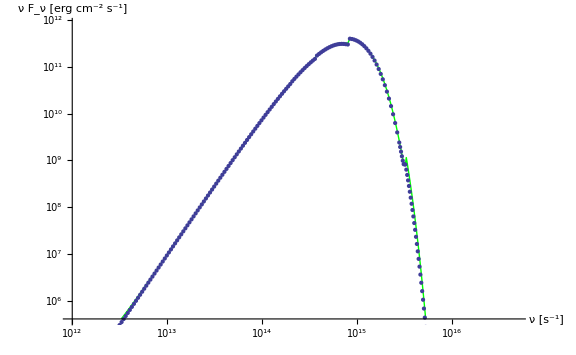

```mathematica
Tp=10^4;
(*Read in  list of opacities*)
o=Opac[mydir<>"/t40_isot/fort.85"];
χ=o[[All, 2, 1]];
freq=o[[All,1]];
(*Scattering opacity*)
μe=0.74;
σ=μe 0.4;
κ=χ;
(*Pure absorption opacity*)
κ=κ-σ;
ϵ=κ;
(*Extinction probability*)
ϵ=κ/(κ+σ);
bb=ν1 B[10^4]/.ν1->freq;
gb=2π  ϵ^(1/2)/(ϵ^(1/2)+1) bb;
Show[PlotF[mydir<>"/t40_isot/fort.13"], ListLogLogPlot[Transpose[{freq, gb}]]]
```

```mathematica
(*dmtot=5;
m0=-3;
logm=Range[m0, dmtot, 8/69]
m=10^logm//N
ρc=10^-11;
Tp=10^4;
ne=0.74 ρc/mp;
atm=Table[{Tp, ne, ρc,0}, {i, 1 70}]//N;
atm=Flatten/@Transpose[{m, atm}];
(*getting the correct z-coordinate*)
atm[[All, -1]]=atm[[All, 1]]/atm[[All,4]];
Row[m, "    "]
(Map[ScientificForm[#,NumberFormat->(SequenceForm[#1,"E",#3]&) ]&,atm[[All, 2;;]], {2}])//Reverse//TableForm*)
```

```mathematica
(*atm= ParseAtm["~/First_Year_Project/tlusty_tar/examples/aleksey_tlusty_runs/tmp/fort.7"];
m=atm[[All, 1]];
o=Opac["~/First_Year_Project/tlusty_tar/examples/aleksey_tlusty_runs/tmp/fort.85"];
μe=mp atm[[All,3]]/atm[[All,4]];
σ=μe 0.4;
σ=σ[[1]];
(*opacities at various frequencies for the outer-most depth point*)
o1=Transpose[{o[[All, 1]],o[[All,2, 1]]}];
κ=o1[[All, 2]]-σ;
ϵ=κ/(κ+σ);
(*Extinction probabilities at the outer most part of the atmosphere*)
ϵ=Map[If[#<0, 0, #]&, ϵ];
freq=o1[[All,1]];
planck=B[Tp]/.{ν1->freq};
ϵ=ϵ[[2;;]];
planck=planck[[2;;]];
flux=(freq//Differences)ϵ^(1/2)/(ϵ^(1/2)+1)planck//Total;
flux=-2 π flux*)
```

```mathematica
(*dat=ReadList["~/First_Year_Project/tlusty_tar/examples/aleksey_tlusty_runs/t40/fort.85", Number, RecordLists->True];
nd=70;
Tp=10600;
(*frequencies*)
ν=Extract[dat, Position[dat, x_/;Length[x]==2]];
ν=ν[[All,2]]
κ=DeleteCases[dat,x_/;Length[x]==2]
κ=κ//Flatten//Partition[#, nd]&
κes=0.4;
tmp= #* Prepend[md//Differences, md[[1]]]&/@κ;
tmp2=FoldList[Plus,0, #]&/@tmp;

tmp3=Nearest[#, 1]&/@tmp2//Flatten;
tmppos=Table[Position[tmp2[[i]], tmp3[[i]]], {i, 1, Length[tmp2]}];
κabs=(Table[Extract[κ[[i]], tmppos [[i]]], {i, 1, Length[tmppos]}]//Flatten)-0.4;
κabs=If[#<0, 0, #]&/@κabs;
ϵ=κabs/(κabs+κes);
gray=Table[{ν[[i]], ϵ[[i]]^(1/2)/(1+ϵ[[i]]^(1/2))B[Tp] ν1/.ν1->ν[[i]]}, {i, 1, Length[ν]}]*)


(*gp2=ListLogLogPlot[gray, Joined->True]*)
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

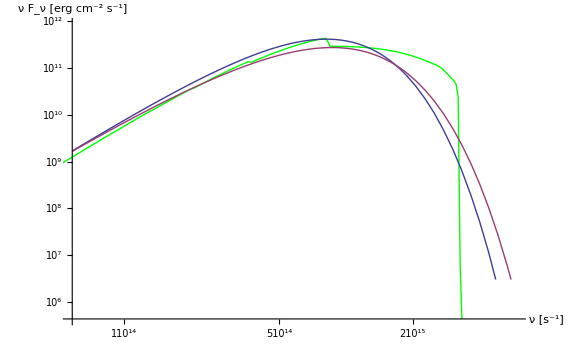

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-Graphics-

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

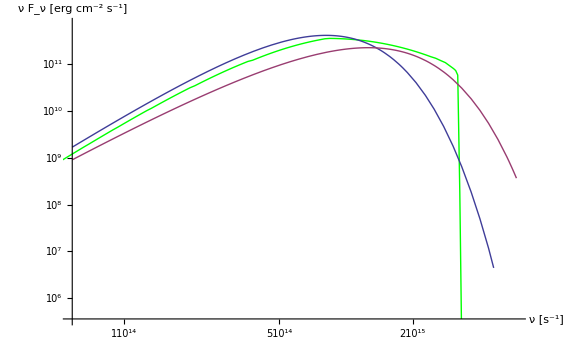

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

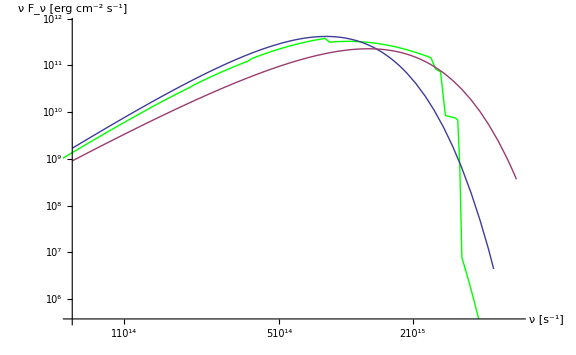

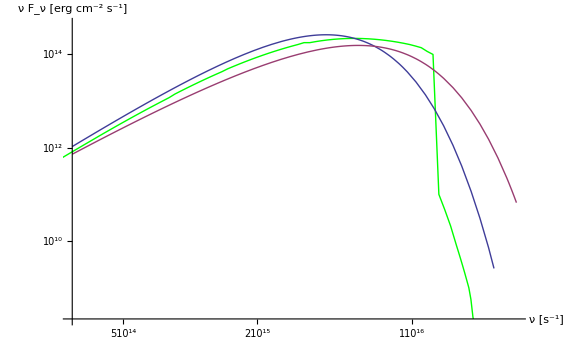

```mathematica
GraybodyCompare[mydir<>"/t40_solar/t40m36q-123/converged"]
GraybodyCompare[mydir<>"/t40_solar/t40m36q-123/converged"]
GraybodyCompare[mydir<>"/t40_solar/t40m56q-143/converged"]
GraybodyCompare[mydir<>"/t40_solar/t40m56q-143/lteconv"]
GraybodyCompare[mydir<>"/t40_solar/t47m58q-86/lteconv"]
```

```mathematica
(*Teff=10^4;
Qg=5.01 10^-13;
m=ParseAtm["~/First_Year_Project/tlusty_tar/examples/aleksey_tlusty_runs/t40_solar/t40m56q-143/converged/fort.7"][[All,1]]
o=Opac["~/First_Year_Project/tlusty_tar/examples/aleksey_tlusty_runs/t40_solar/t40m56q-143/converged/fort.85"]//Reverse;
χ=o//#[[-1,2]]&
ν=o//#[[-1, 1]]&
Transpose[{m, χ}]//ListLogLogPlot
ϵ=GrayBody[Teff, Qg][[3]]/.ν1->ν//Re//ScientificForm
Tp=GrayBody[Teff, Qg][[2]]
*)
```

```mathematica
(*o=Opac["~/First_Year_Project/tlusty_tar/examples/aleksey_tlusty_runs/t40_solar/t40m56q-143/converged/fort.85"];
atm=ParseAtm["~/First_Year_Project/tlusty_tar/examples/aleksey_tlusty_runs/t40_solar/t40m56q-143/converged/fort.7"];
ne=atm[[All,3]];
dens=atm[[All,4]];
z=atm[[All,5]];
T=atm[[All,2]];
δz=z//Differences;
o=o//Reverse;
χ=o[[All,2]];
ν=o[[All,1]];
τ=-#[[2;;]] δz dens[[2;;]]&/@χ;
near=Nearest[#,1]&/@τ;
pos=Table[Position[ τ[[i]], near[[i,1]]], {i, 1, Length[near]}];
(*Total opacity at the photosphere*)
χ=Table[Extract[χ[[i]],pos[[i]]], {i, 1, Length[χ]}]//Flatten;
ne=Table[Extract[ne, pos[[i]]], {i, 1, Length[pos]}]//Flatten;
dens=Table[Extract[dens, pos[[i]]], {i, 1, Length[pos]}]//Flatten;
T=Table[Extract[T, pos[[i]]], {i, 1, Length[pos]}]//Flatten;
μe=ne mp/dens;
σ=μe 0.4;
κ=χ;
ϵ=κ/(κ+σ);
spec=Table[{ν[[i]], ν[[i]](B[T[[i]]]/.{ν1->ν[[i]]})ϵ[[i]]^(1/2)/(1+ϵ[[i]]^(1/2))}, {i, 1, Length[ν]}];
tlustynlte=PlotSpec["~/First_Year_Project/tlusty_tar/examples/aleksey_tlusty_runs/t40_solar/t40m56q-143/converged/fort.14",Green];

pspec=ListLogLogPlot[spec, PlotRange->{{1.8 10^14, 5 10^15},{10^6, 10^12}}, Joined->True];
Show[pspec,tlustynlte]
Manipulate[Module[{gb, planck},
planck=B[Tp]/.ν1->ν;
gb=ListLogLogPlot[Transpose[{ν, ν ϵ^(1/2)/(1+ϵ^(1/2))planck}], PlotRange->{{1.8 10^14, 5 10^15},{10^6, 10^12}}, Joined->True];
Show[{gb,tlustynlte}]]
, {{Tp, 12000}, 10000, 30000}]*)
```

```mathematica
GraybodyCompare2[mydir<>"/t40_solar/t47m58q-86/lteconv"]
```